```mathematica
(* C3.AI COVID CHALLENGE *)
```

```mathematica
(* Sweden *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
type = "Deaths_per_Million";
policy = "H2_Policy";
```

```mathematica
pD0 = 0.6650;
pD1=0.1372;
pD2=0.0598;
pD3=0.1188;
pD4=0.0192;
pD0+pD1+pD2+pD3+pD4
```

1.

```mathematica
(* COnditional Prob *)
```

```mathematica
pD0C6l1=0.783019;
pD1C6l1=0.513441;
pD2C6l1 = 0.00617;
pD3C6l1=0.003106;
pD4C6l1 = 0.01923;
```

```mathematica
pD0C6l0=1-pD0C6l1;
pD1C6l0=1-pD1C6l1;
pD2C6l0 =1-pD2C6l1;
pD3C6l0=1-pD3C6l1;
pD4C6l0=1-pD4C6l1;
```

```mathematica
(* C6 - 1 *)
```

```mathematica
prC6l0 = pD0 pD0C6l0 +  pD1 pD1C6l0+ pD2 pD2C6l0+ pD3 pD3C6l0+ pD4 pD3C6l0
```

0.408051

```mathematica
prC6l1= pD0 pD0C6l1 +  pD1 pD1C6l1+ pD2 pD2C6l1+ pD3 pD3C6l1+ pD4 pD3C6l1
```

0.591949

```mathematica
(* Quantum Prob *)
```

```mathematica
interfC6l0 = Sqrt[pD0 pD0C6l0 pD1 pD1C6l0]Cos[θ00-θ10]+ Sqrt[pD0 pD0C6l0  pD2 pD2C6l0] Cos[θ00-θ20] +  Sqrt[pD0 pD0C6l0  pD3 pD3C6l0] Cos[θ00-θ30]+  Sqrt[ pD0 pD0C6l0  pD4 pD4C6l0] Cos[θ00-θ40]+ 
Sqrt[pD1 pD1C6l0  pD2 pD2C6l0 ] Cos[θ10-θ20]+ Sqrt[pD1 pD1C6l0  pD3 pD3C6l0] Cos[θ10-θ30]+
Sqrt[pD1 pD1C6l0  pD4 pD4C6l0 ]Cos[θ10-θ40]+
Sqrt[pD2 pD2C6l0  pD3 pD3C6l0]  Cos[θ20-θ30] +Sqrt[pD2 pD2C6l0  pD4 pD4C6l0 ]Cos[θ20-θ40]+Sqrt[pD3 pD3C6l0  pD4 pD4C6l0 ]Cos[θ30-θ40];
```

```mathematica
interfC6l1 = Sqrt[pD0 pD0C6l1 pD1 pD1C6l1]Cos[θ01-θ11]+ Sqrt[pD0 pD0C6l1 pD2 pD2C6l1] Cos[θ01-θ21] +  Sqrt[pD0 pD0C6l1  pD3 pD3C6l1] Cos[θ01-θ31]+   Sqrt[ pD0 pD0C6l1  pD4 pD4C6l1] Cos[θ01-θ41]+ 
Sqrt[pD1 pD1C6l1  pD2 pD2C6l1 ] Cos[θ11-θ21]+ Sqrt[pD1 pD1C6l1  pD3 pD3C6l1] Cos[θ11-θ31]+
Sqrt[pD1 pD1C6l1  pD4 pD4C6l1 ]Cos[θ11-θ41]+
Sqrt[pD2 pD2C6l1  pD3 pD3C6l1 ] Cos[θ21-θ31]+Sqrt[pD2 pD2C6l1  pD4 pD4C6l1 ]Cos[θ21-θ41]+Sqrt[pD3 pD3C6l1  pD4 pD4C6l1 ]Cos[θ31-θ41];
```

```mathematica
qprC6l0 = prC6l0 + 2 interfC6l0;
```

```mathematica
qprC6l1= prC6l1 + 2 interfC6l1;
```

```mathematica
qprC6l0Norm = FullSimplify[qprC6l0/(qprC6l0+qprC6l1)];
```

```mathematica
qprC6l1Norm =1-qprC6l0Norm;
(*FullSimplify[qprC6l1/(qprC6l0+qprC6l1)]; *)
```

```mathematica
res = Minimize[{qprC6l0Norm,qprC6l0Norm+qprC6l1Norm == 1},{θ00,θ01,θ10,θ20,θ30,θ40,θ11,θ21,θ31,θ41}]
```

{0.000283684,{θ00→0.10881,θ01→-0.315844,θ10→-1.65395,θ20→1.90559,θ30→-3.48026,θ40→-1.20925,θ11→-0.315844,θ21→-0.315844,θ31→-0.315844,θ41→-0.315844}}

```mathematica
(* Params *)
```

```mathematica
θ10=res[[2]][[3]][[2]];
 θ20=res[[2]][[4]][[2]];
 θ30=res[[2]][[5]][[2]];
 θ40=res[[2]][[6]][[2]];
θ11=res[[2]][[7]][[2]];
θ21=res[[2]][[8]][[2]];
θ31=res[[2]][[9]][[2]];
θ41=res[[2]][[10]][[2]];
```

```mathematica
qprC6l0Norm = FullSimplify[qprC6l0/(qprC6l0+qprC6l1)];
```

```mathematica
qprC6l1Norm =1-qprC6l0Norm;
```

```mathematica
(* Updated probabilities *)
```

```mathematica
{qprC6l0Norm,qprC6l1Norm}
```

{(1.55984-1.54896 Cos[θ00]-0.16921 Sin[θ00])/(4.93312-1.54896 Cos[θ00]+2.39277 Cos[θ01]-0.16921 Sin[θ00]-0.781916 Sin[θ01]),1-(1.55984-1.54896 Cos[θ00]-0.16921 Sin[θ00])/(4.93312-1.54896 Cos[θ00]+2.39277 Cos[θ01]-0.16921 Sin[θ00]-0.781916 Sin[θ01])}

```mathematica
p0 =Plot3D[qprC6l0Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
p1 =Plot3D[qprC6l1Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
Show[p0,p1]
```

-Graphics3D-

```mathematica
fig = StreamDensityPlot[{qprC6l0Norm,qprC6l1Norm},{θ00,-2π,2π},{θ01,-2π,2π},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},10],AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

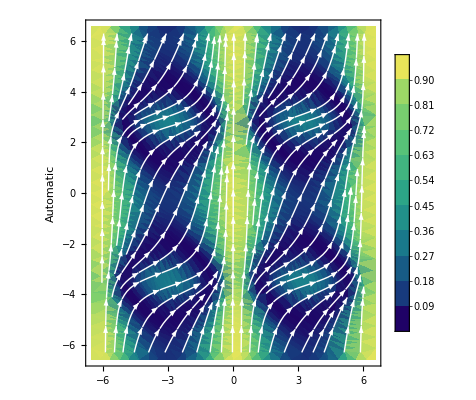

```mathematica
Clear[ θ10,θ20, θ30,θ40, θ11, θ21, θ31,θ41]
```

```mathematica
res = Maximize[{qprC6l0Norm,qprC6l0Norm+qprC6l1Norm == 1},{θ00,θ01,θ10,θ20,θ30,θ40,θ11,θ21,θ31,θ41}]
```

{0.784602,{θ00→-3.03278,θ01→2.82575,θ10→-1.50482,θ20→4.38485,θ30→0.584017,θ40→-1.46307,θ11→1.07557,θ21→0.2242,θ31→1.54998,θ41→0.646562}}

```mathematica
θ10=res[[2]][[3]][[2]];
 θ20=res[[2]][[4]][[2]];
 θ30=res[[2]][[5]][[2]];
 θ40=res[[2]][[6]][[2]];
θ11=res[[2]][[7]][[2]];
θ21=res[[2]][[8]][[2]];
θ31=res[[2]][[9]][[2]];
θ41=res[[2]][[10]][[2]];
```

```mathematica
qprC6l0Norm = FullSimplify[qprC6l0/(qprC6l0+qprC6l1)];
```

```mathematica
qprC6l1Norm =1-qprC6l0Norm;
```

```mathematica
(* Updated probabilities *)
```

```mathematica
{qprC6l0Norm,qprC6l1Norm}
```

{(1.49904+0.698729 Cos[θ00]-1.26494 Sin[θ00])/(3.86404+0.698729 Cos[θ00]+0.886502 Cos[θ01]-1.26494 Sin[θ00]+1.48256 Sin[θ01]),1-(1.49904+0.698729 Cos[θ00]-1.26494 Sin[θ00])/(3.86404+0.698729 Cos[θ00]+0.886502 Cos[θ01]-1.26494 Sin[θ00]+1.48256 Sin[θ01])}

```mathematica
p0 =Plot3D[qprC6l0Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
p1 =Plot3D[qprC6l1Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
Show[p0,p1]
```

-Graphics3D-

```mathematica
fig = StreamDensityPlot[{qprC6l0Norm,qprC6l1Norm},{θ00,-2π,2π},{θ01,-2π,2π},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},10],AxesLabel->Automatic,StreamStyle->{White, Thick}]
```